```mathematica
ClearAll["Global`*"]
```

### Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

#### Helper func

```mathematica
makeErrorData[x_,y_,yErr_]:=Module[{zeList,xy,errorB},
xy=Partition[Riffle[x,y],2];
errorB=Map[ErrorBar,yErr];
zeList=Partition[Riffle[xy,errorB],2]
];
```

```mathematica
Needs["ComputerArithmetic`"]
```

## Ze plot data

```mathematica
time={"21:55:58.049","21:55:58.207","21:55:58.365","21:55:58.523","21:55:58.681","21:55:58.839","21:55:58.997","21:55:59.155","21:55:59.313","21:55:59.471","21:55:59.629","21:55:59.787","21:55:59.945","21:56:00.103","21:56:00.261","21:56:00.419","21:56:00.577","21:56:00.735","21:56:00.893","21:56:01.051","21:56:01.209","21:56:01.367","21:56:01.525","21:56:01.683","21:56:01.841","21:56:01.998","21:56:02.156","21:56:02.314","21:56:02.472","21:56:02.630","21:56:02.788","21:56:02.946","21:56:03.104","21:56:03.262","21:56:03.420","21:56:03.578","21:56:03.736","21:56:03.894","21:56:04.052","21:56:04.210","21:56:04.368","21:56:04.526","21:56:04.684","21:56:04.842","21:56:05.000","21:56:05.158","21:56:05.316","21:56:05.474","21:56:05.632","21:56:05.790","21:56:05.948","21:56:06.106","21:56:06.264","21:56:06.422","21:56:06.580","21:56:06.738","21:56:06.896","21:56:07.053","21:56:07.211","21:56:07.369","21:56:07.527","21:56:07.685","21:56:07.843","21:56:08.001","21:56:08.159","21:56:08.317","21:56:08.475","21:56:08.633","21:56:08.791","21:56:08.949","21:56:09.107","21:56:09.265","21:56:09.423","21:56:09.581","21:56:09.739","21:56:09.897","21:56:10.055","21:56:10.213","21:56:10.371","21:56:10.529","21:56:10.687","21:56:10.845","21:56:11.003","21:56:11.161","21:56:11.319","21:56:11.477","21:56:11.635","21:56:11.793","21:56:11.951","21:56:12.109","21:56:12.266","21:56:12.424","21:56:12.582","21:56:12.740","21:56:12.898","21:56:13.293","21:56:13.451","21:56:13.609","21:56:13.767","21:56:13.925","21:56:14.083","21:56:14.241","21:56:14.399","21:56:14.557","21:56:14.715","21:56:14.873","21:56:15.031","21:56:15.189","21:56:15.347","21:56:15.505","21:56:15.663","21:56:15.821","21:56:15.979","21:56:16.137","21:56:16.295","21:56:16.453","21:56:16.611","21:56:16.769","21:56:16.927","21:56:17.085","21:56:17.243","21:56:17.401","21:56:17.559","21:56:17.717","21:56:17.874","21:56:18.032","21:56:18.190","21:56:18.348","21:56:18.506","21:56:18.664","21:56:18.822","21:56:18.980","21:56:19.138","21:56:19.296","21:56:19.454","21:56:19.612","21:56:19.770","21:56:19.928","21:56:20.086","21:56:20.244","21:56:20.402","21:56:20.560","21:56:20.718","21:56:20.876","21:56:21.034","21:56:21.192","21:56:21.350","21:56:21.508","21:56:21.666","21:56:21.824","21:56:21.982","21:56:22.140","21:56:22.298","21:56:22.456","21:56:22.614","21:56:22.772","21:56:22.930","21:56:23.088","21:56:23.246","21:56:23.404","21:56:23.561","21:56:23.719","21:56:23.877","21:56:24.035","21:56:24.193","21:56:24.351","21:56:24.509","21:56:24.667","21:56:24.825","21:56:24.983","21:56:25.141","21:56:25.299","21:56:25.457","21:56:25.615","21:56:25.773","21:56:25.931","21:56:26.089","21:56:26.247","21:56:26.405","21:56:26.563","21:56:26.721","21:56:26.879","21:56:27.037","21:56:27.195","21:56:27.353","21:56:27.511","21:56:27.669","21:56:27.827","21:56:27.985","21:56:28.143","21:56:28.301","21:56:28.459","21:56:28.617","21:56:28.775","21:56:28.933","21:56:29.091","21:56:29.248","21:56:29.406","21:56:29.564","21:56:29.722" };pots={940.80,940.80,940.80,940.80,1128.96,1379.84,1630.72,1881.60,1881.60,1630.72,1881.60,1630.72,2257.92,2257.92,1630.72,1630.72,1630.72,1881.60,1128.96,1128.96,2257.92,2759.68,2759.68,3261.44,3261.44,3763.20,3763.20,3763.20,3261.44,3372.32,3261.44,2759.68,2759.68,2759.68,2257.92,2257.92,2257.92,2759.68,3261.44,3261.44,3763.20,3763.20,3763.20,3763.20,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,5600.00,4515.84,4515.84,5519.36,5790.40,5519.36,5519.36,5519.36,5679.52,6522.88,6522.88,6522.88,6522.88,5519.36,5519.36,5519.36,5519.36,5519.36,5741.12,5519.36,5519.36,5519.36,5519.36,6522.88,6522.88,6522.88,6522.88,6522.88,6522.88,6522.88,5519.36,5519.36,5519.36,5519.36,5519.36,5519.36,6522.88,6522.88,6522.88,6522.88,6522.88,6522.88,6522.88,6793.92,6522.88,6522.88,6522.88,6522.88,6522.88,6522.88,6522.88,6522.88,6522.88,6522.88,6522.88,6522.88,13619.20,6522.88,6522.88,6522.88,7526.40,7526.40,7526.40,7526.40,7526.40,7526.40,7526.40,7661.92,7846.72,9031.68,9004.80,9031.68,9573.76,9031.68,9770.88,9475.20,9216.48,9401.28,9031.68,9031.68,9031.68,9031.68,7526.40,8167.04,7526.40,7526.40,7526.40,7526.40,7526.40,7526.40,7526.40,7637.28,7526.40,7526.40,7526.40,7526.40,6522.88,6522.88,6522.88,6522.88,6522.88,6522.88,6522.88,6522.88,6522.88,7526.40,7526.40,6522.88,6522.88,6522.88,5519.36,6522.88,5519.36,5519.36,5519.36,5519.36,5519.36,5519.36,5519.36,5519.36,5519.36,4515.84,3763.20,3261.44,4515.84,3763.20,3261.44,3261.44,3763.20,3763.20,4515.84,3261.44,3763.20,3763.20,3763.20,3763.20,3763.20,3763.20,3763.20,3763.20,3763.20,3763.20,3763.20,3763.20,3763.20,3763.20}; curs={1.180,1.084,1.408,1.070,1.291,1.462,1.789,1.543,1.811,1.989,1.752,1.685,2.180,2.242,1.934,2.144,2.122,2.331,1.468,2.000,2.985,2.777,2.219,2.840,2.784,2.268,2.091,1.989,2.815,3.020,3.131,3.012,2.884,2.956,2.718,2.860,3.325,2.920,2.243,2.563,2.835,2.116,1.388,1.265,1.269,1.228,1.115,1.179,1.137,1.222,1.141,1.081,1.106,1.111,1.068,1.092,1.244,1.063,1.132,1.222,1.314,1.222,1.249,1.247,1.250,1.353,1.105,1.195,1.234,1.301,1.224,1.174,1.056,1.106,1.120,1.186,1.185,1.271,1.292,1.324,1.208,1.220,1.238,1.229,1.224,1.316,1.234,1.262,1.172,1.124,1.032,1.020,1.077,1.009,1.065,1.737,1.670,1.704,1.622,1.744,1.651,1.716,1.800,1.659,1.647,1.676,1.676,1.694,1.602,1.637,1.754,1.756,1.876,1.995,2.183,2.178,2.176,2.189,2.266,2.274,2.201,2.227,2.264,2.276,2.179,2.148,2.277,2.067,2.106,2.197,2.300,2.234,2.281,2.237,2.251,2.337,2.111,2.041,1.985,1.994,1.980,1.979,2.017,2.021,1.979,1.908,2.051,1.856,1.934,1.672,1.702,1.710,1.648,1.490,1.408,1.430,1.428,1.495,1.483,1.608,1.532,1.449,1.249,1.196,1.131,1.028,1.021,1.044,0.988,0.914,0.863,0.879,1.031,0.918,0.808,0.727,0.487,0.482,0.661,0.626,0.604,0.669,0.679,0.504,0.551,0.535,0.580,0.622,0.613,0.590,0.610,0.617,0.621,0.644,0.628,0.639,0.632,0.630,0.629,0.609}; curErrs={0.026,0.026,0.028,0.025,0.031,0.027,0.030,0.028,0.032,0.032,0.035,NaN,0.034,NaN,0.035,0.035,0.036,0.036,0.030,NaN,0.043,0.040,0.041,0.041,0.043,0.052,0.058,0.036,0.040,0.045,0.045,0.042,0.042,0.042,0.039,0.043,0.042,0.041,NaN,0.043,0.047,0.048,0.067,0.080,0.098,0.106,0.135,0.141,0.131,0.155,0.130,0.159,0.116,0.111,0.152,0.127,0.137,0.148,0.153,0.138,0.123,0.248,0.124,0.142,0.129,0.106,0.148,0.158,0.142,0.140,0.128,0.186,0.126,0.141,0.160,0.160,0.098,0.133,0.149,0.142,0.133,0.136,0.176,0.116,0.182,0.137,0.155,0.118,0.164,0.149,0.149,0.128,0.128,0.124,0.132,0.504,0.327,0.209,0.229,0.325,0.326,0.308,0.257,0.212,0.209,0.346,0.356,0.317,0.224,0.257,0.295,0.284,0.274,0.356,0.341,0.290,0.308,0.320,0.365,0.295,0.258,0.356,0.279,0.288,0.237,0.924,0.349,0.311,0.220,0.235,0.314,0.213,0.216,0.245,0.194,0.243,0.216,0.206,0.198,0.218,0.232,0.240,0.305,0.287,0.209,0.262,0.237,0.253,0.317,0.263,0.327,0.451,0.448,0.333,0.236,0.373,0.408,0.399,0.386,0.643,0.811,0.235,0.270,0.413,0.242,0.223,0.227,0.264,0.140,0.171,0.229,0.181,0.206,0.285,0.390,0.167,0.226,0.274,0.275,0.201,0.249,0.125,0.170,NaN,0.033,0.032,0.032,0.032,0.031,0.034,0.034,0.066,0.034,0.035,0.037,0.037,0.033,0.037,NaN,-NaN}; jes={1.911,1.765,2.177,1.912,2.359,2.641,3.381,3.131,3.845,4.004,3.996,3.739,4.708,4.821,3.767,4.167,3.967,4.401,2.743,3.900,6.779,7.262,6.825,8.663,9.429,8.797,8.280,7.425,9.793,9.845,9.595,8.452,7.589,7.527,6.500,6.380,7.798,7.869,7.161,8.195,9.289,7.501,5.746,5.465,5.572,5.503,5.045,5.258,5.013,5.499,5.210,4.873,5.175,5.049,4.942,4.953,5.764,5.116,5.598,6.214,7.180,7.060,7.422,7.431,7.572,8.089,6.616,7.041,6.919,7.032,6.248,5.885,5.176,5.742,6.412,7.967,7.869,8.496,8.543,8.631,7.942,8.433,8.595,8.097,7.922,8.068,7.198,7.407,7.180,7.649,6.962,6.825,7.479,6.920,7.424,13.274,12.718,12.894,12.340,13.269,12.041,12.531,13.353,11.664,11.150,11.529,11.602,11.391,10.837,10.993,12.015,12.414,13.019,14.086,16.172,16.304,16.827,16.794,18.019,18.328,17.094,17.115,17.519,18.547,17.414,17.289,18.189,16.624,17.261,17.636,19.038,18.464,18.907,18.512,18.186,17.378,16.834,16.177,15.561,15.438,15.669,15.793,15.626,15.642,15.263,14.242,15.625,13.767,14.785,12.255,12.408,12.789,12.177,11.332,9.984,10.374,10.598,11.378,11.360,12.338,11.167,10.704,8.677,8.130,7.471,6.676,7.084,6.987,6.779,6.273,5.831,5.970,6.714,5.951,5.138,4.314,2.522,2.376,3.892,3.608,3.595,3.870,4.070,3.021,3.314,3.133,3.436,3.699,3.603,3.425,3.545,3.727,3.720,3.886,3.967,3.937,3.730,3.681,3.837,3.474}; jeErrs={3.474,1.471,NaN,1.556,8.590,1.827,2.030,1.259,-NaN,-NaN,2.202,NaN,2.834,NaN,1.411,4.996,8.469,3.787,5.449,NaN,5.696,1.556,1.993,3.756,2.026,1.741,3.127,1.822,NaN,1.963,-NaN,1.754,-NaN,1.862,-NaN,8.310,19.847,3.311,-NaN,2.019,2.339,1.048,0.994,1.567,1.229,-NaN,1.517,1.546,1.743,1.804,2.282,2.060,1.648,1.535,2.000,1.430,-NaN,2.078,2.092,12.633,2.787,1.502,1.866,2.392,2.087,1.867,2.927,2.156,1.981,2.057,1.637,2.621,1.571,1.873,2.547,6.401,2.019,2.813,4.488,2.252,2.151,2.376,2.880,2.081,3.360,2.475,4.283,2.798,4.660,3.872,19.425,3.171,1.998,3.339,2.064,10.052,6.445,4.197,4.082,-NaN,7.112,5.907,5.807,-NaN,5.079,6.817,7.502,6.893,-NaN,4.703,6.563,7.267,6.427,7.184,7.428,6.445,6.656,6.515,8.616,7.580,5.273,-NaN,6.674,-NaN,5.743,5.732,10.496,13.601,7.357,4.716,7.507,5.107,5.093,5.294,-NaN,3.829,-NaN,5.021,4.820,-NaN,5.190,-NaN,13.652,6.001,4.127,5.871,9.917,11.026,-NaN,6.492,18.320,-NaN,8.783,8.580,11.922,6.976,8.934,-NaN,68.169,14.582,25.760,-NaN,4.638,11.963,34.587,3.648,6.367,15.430,3.932,3.426,14.176,4.035,20.510,11.499,124.395,9.624,3.358,3.554,10.959,6.399,4.371,-NaN,2.913,NaN,0.939,-NaN,0.806,0.839,-NaN,0.730,0.760,0.992,1.305,0.890,0.804,0.736,0.924,0.832,NaN,-NaN}; gaussbulkEs={1229.81,1167.98,1407.58,1544.17,1521.77,1491.10,1878.59,1459.86,1947.74,1966.34,2254.84,1858.82,1869.87,1817.82,1881.60,1260.55,1545.36,2622.80,2667.49,3197.98,3251.60,3779.17,4223.66,4287.45,3252.98,3894.86,3124.23,2596.80,2515.13,2960.73,3233.82,3886.73,3477.17,3962.11,3261.44,3352.22,3345.87,3363.83,3565.19,4723.06,4742.63,4734.50,3470.67,3517.34,5055.60,5020.98,3949.07,5939.78,6067.84,4153.73,5678.75,6044.34,7002.79,6741.32,7064.90,4064.15,6031.73,5907.43,3763.38,3804.29,5726.36,5953.81,6345.45,5926.27,5994.81,4515.84,4634.53,7097.49,5093.79,4516.02,7532.79,6225.09,4576.12,4468.98,4042.32,3813.20,3763.20,5946.06,7875.10,4515.84,7021.12,4597.10,4535.05,8241.35,7504.57,4516.99,6930.20,4515.84,7608.33,4991.74,4665.35,4515.84,4755.94,4909.33,4707.40,7160.40,7588.20,7201.20,4522.35,4515.99,4924.21,4993.19,8561.80,8350.42,5545.80,5521.79,5519.36,8307.20,5716.02,8095.83,8266.90,5949.78,8278.22,5982.81,5935.74,8254.24,9994.86,8530.13,8811.47,6065.92,6057.69,7929.87,8129.86,5519.36,5519.36,5555.98,8122.66,8809.56,8409.44,8335.67,5519.36,5520.31,5519.36,8181.92,8094.02,5519.36,6732.25,7171.38,7256.55,4871.13,7930.81,7101.08,7428.73,7371.91,7921.22,6884.48,9123.05,8485.68,4515.84,6710.07,7646.23,6480.94,3810.69,6518.79,6908.06,3768.80,6417.75,6481.21,6428.26,6226.05,6517.28,5892.79,5805.72,4500.60,3626.41,2269.61,2287.99,4515.83,2529.50,2257.92,4515.82,4515.17,4168.52,5202.07,4515.84,5196.53,2759.68,2759.68,5100.91,4722.49,5467.18,5141.66,5461.62,2759.68,3234.44,2257.92,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84}; kappabulkEs={1238.95,1300.00,1287.71,1281.33,1274.64,1236.94,1363.78,1475.87,1796.63,1749.53,1835.04,1676.39,1464.76,1692.93,1582.11,1249.17,1497.72,2569.71,2955.04,3071.21,2882.65,3575.44,4142.55,4211.58,3314.30,3248.28,3578.98,2921.11,2472.77,3406.28,3400.62,3672.22,3917.81,3815.43,4469.42,4907.37,4589.26,5418.86,4814.79,4746.34,4631.26,4611.44,4697.46,4570.54,5011.44,4715.92,5426.24,5084.14,5812.94,5724.75,5409.14,5762.53,6084.45,5965.84,5715.84,5513.20,5613.20,5259.01,5038.07,5086.21,5564.58,5360.08,5613.70,5524.14,5401.97,6231.87,6166.67,6715.87,6315.84,6565.84,5865.84,5663.20,5614.47,5513.20,5663.20,5570.55,5924.77,5463.20,6094.14,6194.43,5977.72,6428.86,5915.84,6515.84,5794.69,6211.50,6610.83,6354.79,6476.06,6443.84,5691.42,6303.63,6115.84,6115.84,6039.83,6104.34,5965.84,5935.90,6215.65,6465.84,6665.84,6115.84,7358.89,7657.11,7769.36,6862.22,7608.92,6819.36,6893.56,6632.59,7819.36,7019.36,7719.36,7569.36,7536.14,7418.33,9022.88,7015.87,6816.07,7569.36,7719.36,7737.38,7619.36,7229.69,7234.91,7223.16,7910.18,7563.02,7419.36,7769.36,7269.36,7369.36,6662.06,7836.21,7440.07,6719.36,6300.32,6215.84,6353.18,6315.84,6198.32,6275.11,5565.84,6139.05,6264.74,6579.04,7704.02,7085.13,6215.84,5815.84,6072.77,5349.56,5269.26,5012.94,5062.93,5373.51,5268.60,5273.53,5317.76,4813.20,4963.46,5142.92,4624.26,3551.91,3207.92,3341.39,3407.24,2858.76,3541.95,3294.27,3257.92,3154.82,2683.66,3779.58,2257.92,3625.15,3043.45,2785.28,3798.41,3950.47,2759.68,2759.68,2774.12,3763.64,3999.33,2257.92,3335.17,3335.17,3335.17,3335.17,3335.17,3335.17,3335.17,3335.17,3335.17,3335.17,3335.17,3335.17,3335.17,3335.17};
```

### Data for first and second portions of arc in which we are interested

```mathematica
inds1=Range[43,95];
inds2=Range[75,91];
inds3={3,4}~Join~inds2;
```

Current data

```mathematica
{plotData1,plotData2,plotData3}=(Partition[Riffle[pots[[#]],curs[[#]]],2])&/@{inds1,inds2,inds3};
```

```mathematica
{errorData1,errorData2,errorData3}=(makeErrorData[pots[[#]],curs[[#]],curErrs[[#]]])&/@{inds1,inds2,inds3};
```

```mathematica
{plotDataWts1,plotDataWts2,plotDataWts3}=(1/(curErrs[[#]])^2)&/@{inds1,inds2,inds3};
```

Energy flux data

```mathematica
{jeData1,jeData2,jeData3}=(Partition[Riffle[pots[[#]],jes[[#]]],2])&/@{inds1,inds2,inds3};
```

### Lil plot to check out J-V relation on the fly

```mathematica
ind1End=30;Manipulate[ErrorListPlot[(makeErrorData[gaussbulkEs[[#1;;#2]],curs[[#1;;#2]],curErrs[[#1;;#2]]])&[ind1,ind2],PlotRange->{{500,10000},{0,4}},Epilog->Style[Text[StringJoin@Riffle[time[[{ind1,ind2}]],"–"],Scaled[{0.05,0.95}],{-1,1}],24],ImageSize->700],{ind1,Range[1,ind1End]},{{ind2,Length@pots},Range[ind1End+1,Length@pots]}]
```

```mathematica
Integrate[stuff,{vz,0,∞},{vperp,0,∞},Assumptions-> (ω∈Complexes&&kz∈Reals)]
```

### Lil plot to check out energy flux–voltage relation on the fly

```mathematica
ind1End=80;Manipulate[ErrorListPlot[(makeErrorData[pots[[#1;;#2]],jes[[#1;;#2]],jeErrs[[#1;;#2]]])&[ind1,ind2],PlotRange->{{0,8000},{0,10}},Epilog->Style[Text[StringJoin@Riffle[time[[{ind1,ind2}]],"–"],Scaled[{0.05,0.95}],{-1,1}],24],ImageSize->700],{ind1,Range[1,ind1End]},{{ind2,Length@pots},Range[ind1End+1,Length@pots]}]
```

## Nonlinear fits for first portion of arc

### First, my original, from-the-hip prediction

```mathematica
reg1={Tm-> 300,RB-> 4,nm-> 1};
```

```mathematica
at1=(JVMaxwellian[pot,RB,Tm,nm]/.reg1)
```

1.84974 (1-(3 ⅇ^(-pot/900))/4)

### Now the actual fits

```mathematica
kConstraints={0.01<kFitN<10,400<kFitT<4000,3<kFitRB<10000,1.51<kFitKappa<4};
gConstraints={0.01<gFitN<10,400<gFitT<4000,3<gFitRB<10000};
```

```mathematica
kModel = JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModel = JVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFit=NonlinearModelFit[plotData1,{kModel,kConstraints},{{kFitN,1},{kFitT,300},{kFitRB,10},{kFitKappa,4}},pot,Weights->plotDataWts1]
```

FittedModel[1.22036 (1-0.666668/(1+0.000500008 pot)^2.99994)]

```mathematica
gFit=NonlinearModelFit[plotData1,{gModel,gConstraints},{{gFitN,1},{gFitT,300},{gFitRB,10}},pot,Weights->plotDataWts1]
```

FittedModel[1.20435 (1-0.666668 ⅇ^(-0.00124998 pot))]

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestN,kBestT,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*plotDataWts1]/kDOF}
```

{0.800609,400.002,3.00001,3.99994,0.678201}

```mathematica
{gBestN,gBestT,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*plotDataWts1]/gDOF}
```

{0.75181,400.003,3.00001,0.640122}

```mathematica
kFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.800609 | 65.1461 | 0.0122894 | 0.990245
kFitT | 400.002 | 945822. | 0.000422915 | 0.999664
kFitRB | 3.00001 | 3850.17 | 0.000779189 | 0.999381
kFitKappa | 3.99994 | 956.261 | 0.00418289 | 0.99668

```mathematica
gFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 0.75181 | 22.8478 | 0.0329051 | 0.973881
gFitT | 400.003 | 99526.7 | 0.00401905 | 0.996809
gFitRB | 3.00001 | 464.301 | 0.00646136 | 0.99487

### Ze plot

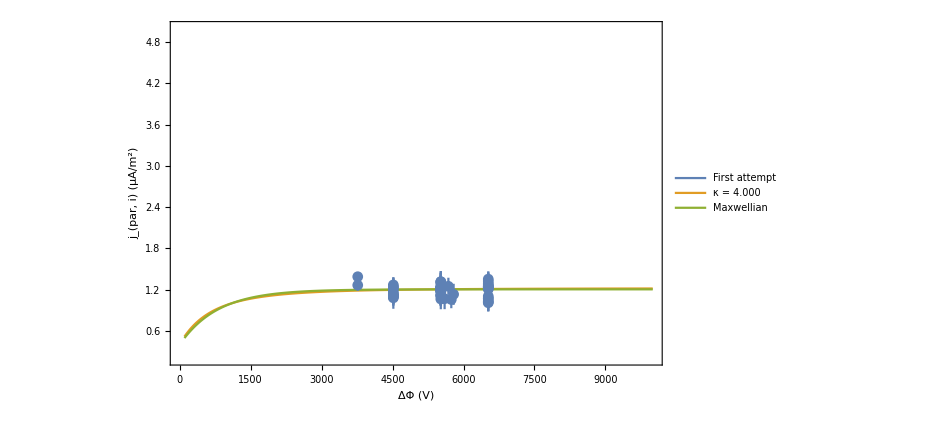

```mathematica
Show[Plot[{at1,kFit[pot],gFit[pot]},{pot,100,10000},PlotRange->{{0,10000},{0.2,5}},PlotLegends->((Style[#,20])&/@{"First attempt",StringForm["κ = `1`",NumberForm[kBestKappa,{3,3}]],"Maxwellian"}),Frame->True,FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->700,FrameStyle->(FontSize->18)],ErrorListPlot[errorData1]]
```

## Linear model for second half of arc

```mathematica
lm=LinearModelFit[plotData2,x,x,Weights->plotDataWts2]
```

FittedModel[0.571783+0.000828171 x]

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.571783 | 0.209522 | 2.72899 | 0.0155285
x | 0.000828171 | 0.000104376 | 7.93453 | 9.52667×10^-7

```mathematica
Kmeas=(lm["BestFitParameters"])[[2]]
```

0.000828171

```mathematica
lm["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
lm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
1 | 0.571783 | 0.209522 | {0.125197,1.01837}
x | 0.000828171 | 0.000104376 | {0.000605699,0.00105064}

```mathematica
lm["AdjustedRSquared"]
```

0.794758

#### See it

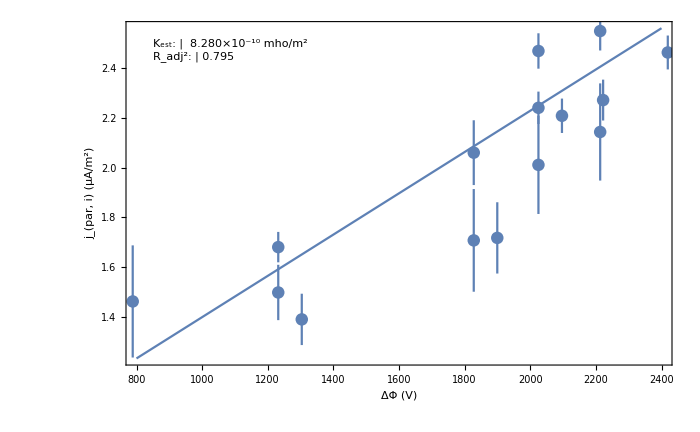

```mathematica
Show[Plot[lm[x],{x,800,2400},Frame->True,FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->700,FrameStyle->(FontSize->18),Epilog->Inset[TextGrid[Map[(Style[#,18])&,{{StringForm["K_est:"],StringForm[" `1` mho/m^2",NumberForm[Kmeas*1*^-6,{3,3},ScientificNotationThreshold->{-2,2}]]},{StringForm["R_adj^2:"],NumberForm[lm["AdjustedRSquared"],{3,3}]}},{2}]],Scaled[{0.05,0.95}],{-1,1}]],ErrorListPlot[errorData2]]
```

### Assess it

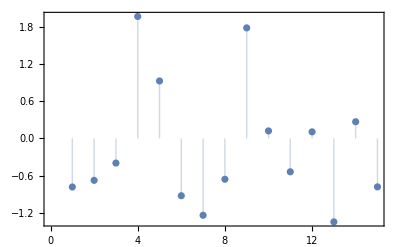

```mathematica
ListPlot[lm["StandardizedResiduals"],Frame->True,Filling->Axis]
```

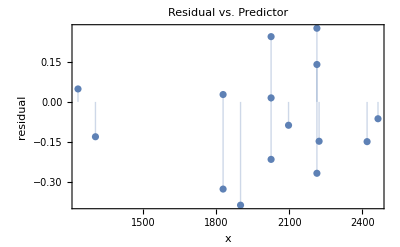

```mathematica
ListPlot[Transpose[{pots[[inds2]],lm["FitResiduals"]}],Frame->True,Filling->0,FrameLabel->{"x","residual"},PlotLabel->"Residual vs. Predictor"]
```

## Artificially combine parts of each

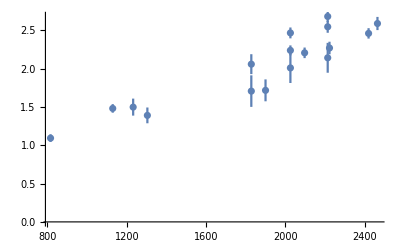

```mathematica
ErrorListPlot[errorData3]
```

## Simultaneously fit both sets of data, allowing RB to be different for each

```mathematica
RBinit=kBestRB;Tminit=kBestT;nminit=kBestN;kappainit=kBestKappa;
```

```mathematica
combDat = Join[plotData1/.{x_,y_}->{1,x,y},plotData2/.{x_,y_}->{2,x,y}];
```

```mathematica
combWts=plotDataWts1~Join~plotDataWts2;
```

```mathematica
kCombFitModel[set_,pot_,kFitRB1_,kFitRB2_,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB1,kFitT,kFitN,kFitKappa],set==2,Evaluate@JVKappa[pot,kFitRB2,kFitT,kFitN,kFitKappa]]
```

```mathematica
gCombFitModel[set_,pot_,gFitRB1_,gFitRB2_,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB1,gFitT,gFitN],set==2,Evaluate@JVMaxwellian[pot,gFitRB2,gFitT,gFitN]]
```

```mathematica
kCombConstraints={1<kFitRB1<300,1<kFitRB2<500,50<kFitT<500,0.1<kFitN<10,1.51<kFitKappa<35};
gCombConstraints={1<gFitRB1<300,1<gFitRB2<500,50<gFitT<500,0.1<gFitN<10};
```

```mathematica
kCombFit=NonlinearModelFit[combDat,{kCombFitModel[set,pot,kFitRB1,kFitRB2,kFitT,kFitN,kFitKappa],kCombConstraints},{{kFitRB1,3},{kFitRB2,10},{kFitT,300},{kFitN,1},{kFitKappa,5}},{set,pot},Weights->combWts]
```

FittedModel[Which[set==1,(«1»)/(«1»),set==2,(0.0266987 0.834972 «19» «1» (1-(1-1/(«19»)) ((«1»«1»)^(«1»)) Gamma[1+35.])/((1-1/35.) («18»)^(3/2) Gamma[-1/2+35.])]]

```mathematica
gCombFit=NonlinearModelFit[combDat,{gCombFitModel[set,pot,gFitRB1,gFitRB2,gFitT,gFitN],gCombConstraints},{{gFitRB1,3},{gFitRB2,10},{gFitT,300},{gFitN,1}},{set,pot},Weights->combWts]
```

FittedModel[Which[set==1,0.0266987 0.777027 («1») «18» √142.278,set==2,0.0266987 0.777027 (1-ⅇ^(-pot/((-1+«19») «19»)) (1-1/12.7063)) 12.7063 √142.278]]

```mathematica
kCombDOF=Length[combDat[[;;,1]]]-4;
```

```mathematica
gCombDOF=Length[combDat[[;;,1]]]-3;
```

```mathematica
{kCombRB1,kCombRB2,kCombT,kCombN,kCombKappa,kCombChi2red}=Values@kCombFit["BestFitParameters"]~Join~{Total[(kCombFit["FitResiduals"])^2*combWts]/kCombDOF}
```

{6.17622,10.7058,187.539,0.834972,35.,6.12727}

```mathematica
{gCombRB1,gCombRB2,gCombT,gCombN,gCombChi2red}=Values@gCombFit["BestFitParameters"]~Join~{Total[(gCombFit["FitResiduals"])^2*combWts]/gCombDOF}
```

{7.52797,12.7063,142.278,0.777027,5.8886}

```mathematica
RBinit1=gCombRB1;RBinit2=gCombRB2;Tminit=gCombT;nminit=gCombN;
```

### Mess ‘round

```mathematica
Manipulate[Row[{Manipulate[Show[Plot[{JVMaxwellian[pot,RB1,Tm,nm],JVKappa[pot,RB1,Tm,nm,kappa1]},{pot,100,3000},PlotRange->{Full,{0.5,4}},PlotLegends->{"Maxwellian",StringForm["κ = `1`",NumberForm[kappa1,{3,1}]]},FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->500,FrameStyle->(FontSize->18)],ErrorListPlot[errorData1]],{{RB1,RBinit1},1.01,300},{{kappa1,kappainit},1.501,35}],Manipulate[Show[Plot[{JVMaxwellian[pot,RB2,Tm,nm],JVKappa[pot,RB2,Tm,nm,kappa2]},{pot,100,3000},PlotRange->{Full,{0.5,4}},PlotLegends->{"Maxwellian",StringForm["κ = `1`",NumberForm[kappa2,{3,1}]]},FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->500,FrameStyle->(FontSize->18)],ErrorListPlot[errorData2]],{{RB2,RBinit2},1.01,300},{{kappa2,kappainit},1.501,35}]}],{{Tm,Tminit},3,500},{{nm,nminit},0.1,5}]
```

ListPlot::lpn: errorData1 is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[errorData1,{},Method→{OptimizePlotMarkers→False}]].

ListPlot::lpn: errorData2 is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[errorData2,{},Method→{OptimizePlotMarkers→False}]].

ListPlot::lpn: errorData1 is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[errorData1,{},Method→{OptimizePlotMarkers→False}]].

ListPlot::lpn: errorData2 is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[errorData2,{},Method→{OptimizePlotMarkers→False}]].

### Just tell ‘em, Hammer

```mathematica
combRepl={RB1->gCombRB1,RB2->gCombRB2,Tm->gCombT,nm->gCombN,kappa1->kCombKappa};
```

```mathematica
parNames={"T_m : ","n_m : ","R_B : "};
vals1=MapThread[NumberForm,{({Tm,nm,RB1}/.combRepl),{{3,0},{3,2},{3,1}}}];
vals2=MapThread[NumberForm,{({Tm,nm,RB2}/.combRepl),{{3,0},{3,2},{3,1}}}];
```

```mathematica
parTable1=Text[Grid[Transpose[{parNames,vals1}],Alignment->".",Spacings->{0,2},ItemStyle->Directive[FontSize->18]]];
parTable2=Text[Grid[Transpose[{parNames,vals2}],Alignment->".",Spacings->{0,2},ItemStyle->Directive[FontSize->18]]];
```

```mathematica
title1=StringJoin@Riffle[StringDrop[time[[inds1[[{1,-1}]]]],11],"–"]
title2=StringJoin@Riffle[StringDrop[time[[inds2[[{1,-1}]]]],11],"–"]
```

09:26:11.332–09:26:22.708

09:26:56.837–09:27:06.950

```mathematica
seg1Plotp1=Plot[Evaluate@(({JVMaxwellian[pot,RB1,Tm,nm],JVKappa[pot,RB1,Tm,nm,kappa1]})/.combRepl),{pot,100,3000},PlotRange->{Full,{0.5,2.5}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa1/.combRepl),{3,1}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["Segment 1 (`1`)",title1],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],Epilog->Inset[parTable1,Scaled[{0.1,0.8}]]];
```

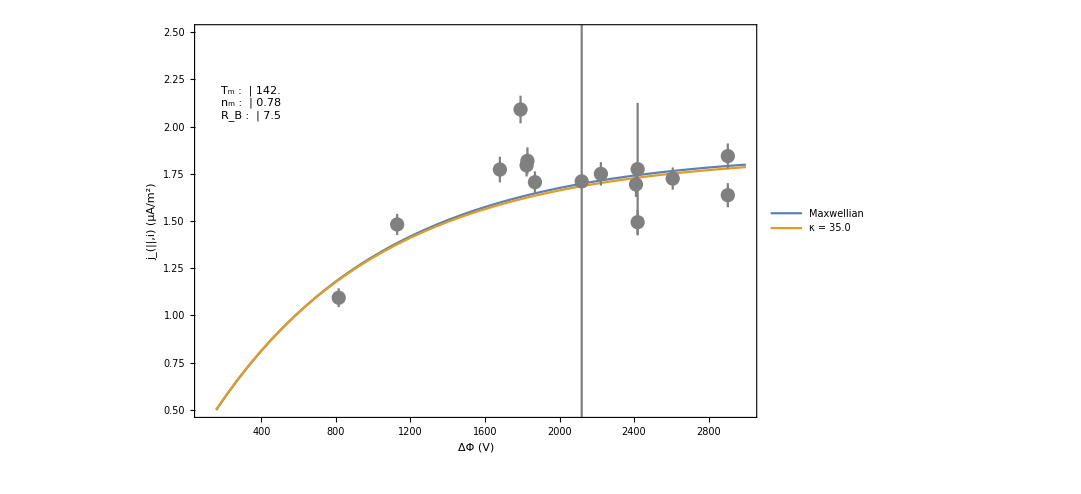

```mathematica
seg1Plot=Show[seg1Plotp1,ErrorListPlot[errorData1,PlotStyle->Gray]]
```

```mathematica
seg2Plotp1=Plot[Evaluate@(({JVMaxwellian[pot,RB2,Tm,nm],JVKappa[pot,RB2,Tm,nm,kappa1]})/.combRepl),{pot,100,3000},PlotRange->{Full,{1.0,3}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa1/.combRepl),{3,1}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["Segment 2 (`1`)",title2],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],Epilog->Inset[parTable2,Scaled[{0.1,0.8}]]];
```

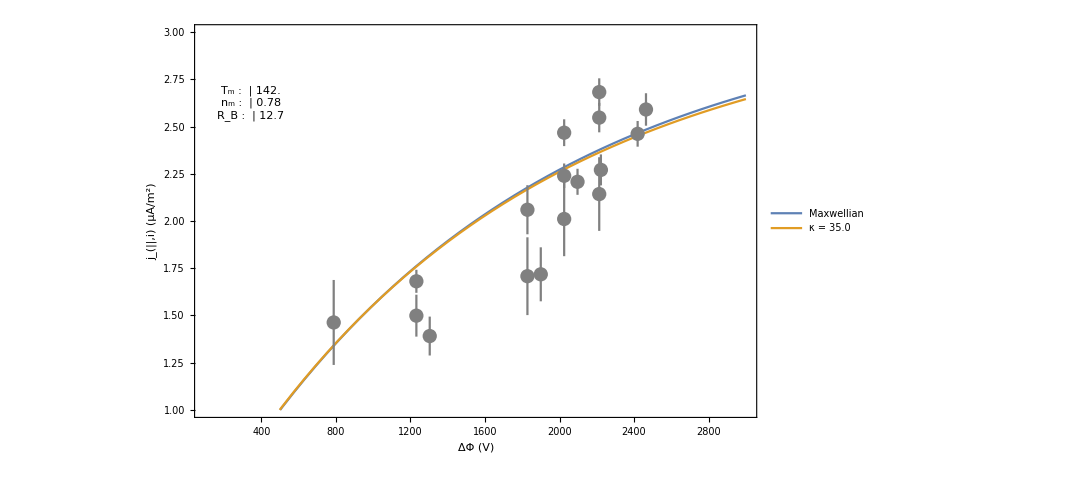

```mathematica
seg2Plot=Show[seg2Plotp1,ErrorListPlot[errorData2,PlotStyle->Gray]]
```

```mathematica
seg2Plotp1=Plot[Evaluate@(({JVMaxwellian[pot,RB2,Tm,nm],JVKappa[pot,RB2,Tm,nm,kappa1]})/.combRepl),{pot,100,3000},PlotRange->{Full,{1.0,3}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa1/.combRepl),{3,1}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["Segment 2 (`1`)",title2],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],Epilog->Inset[parTable2,Scaled[{0.1,0.8}]]];
```

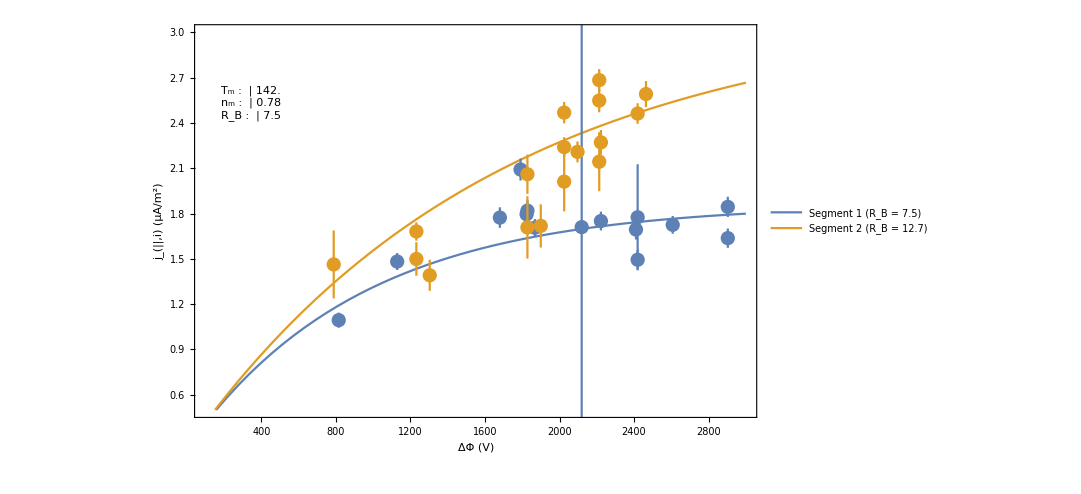

```mathematica
seg2Plot=Show[Plot[Evaluate@(({JVMaxwellian[pot,RB1,Tm,nm],JVMaxwellian[pot,RB2,Tm,nm]})/.combRepl),{pot,100,3000},PlotRange->{Full,{0.5,3}},PlotLegends->Map[(Style[#,23])&,MapThread[(StringForm["Segment `1` (R_B = `2`)",#1,NumberForm[#2,{3,1}]])&,({{"1","2"},{RB1,RB2}}/.combRepl)]],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style["Combined Segments",Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],Epilog->Inset[parTable1,Scaled[{0.1,0.8}]]],ErrorListPlot[{errorData1,errorData2}]]
```